0.005

3.17×10^-6

6.8×10^-7

0.025

2.57×10^-6

3.7×10^-7

0.05

2.6×10^-6

3.3×10^-7

0.075

1.87×10^-6

2.6×10^-7

0.105

1.76×10^-6

2.4×10^-7

0.14

1.63×10^-6

2.2×10^-7

0.18

1.76×10^-6

2.2×10^-7

0.225

1.97×10^-6

2.4×10^-7

0.265

2.×10^-6

3.2×10^-7

0.295

1.07×10^-6

2.8×10^-7

0.335

3.4×10^-7

9.×10^-8

0.39

1.2×10^-7

4.×10^-8

0.53

6.×10^-8

2.×10^-8

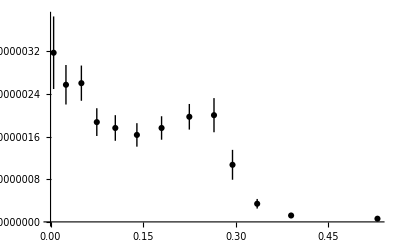

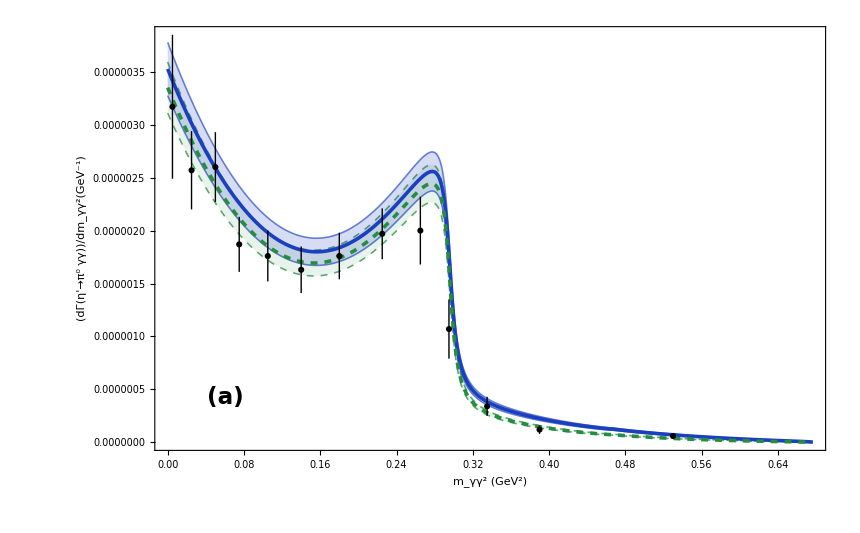

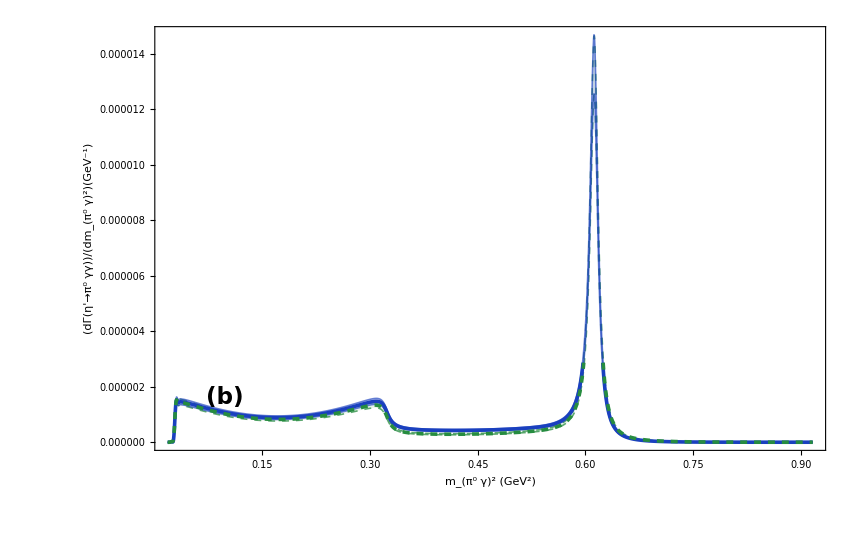

etaPrime_pi0_gamma_gamma_spectrum.pdf

etaPrime_pi0_gamma_spectrum.pdf

<|WidthSM→6.80.510^-7,BranchingSM→0.003590.00027,WidthSMPlusVB→7.30.510^-7,BranchingSMPlusVB→0.003880.00030,WidthPureContinuousVB2→7.21.910^-9,BranchingPureContinuousVB2→0.0000390.000010,PureContinuousVB2Fraction→0.00990.0024,WidthOnShellEffective→7.20.510^-7,BranchingOnShellEffective→0.003850.00029,OnShellEffectiveFraction→0.99010.0024,Yukawa2Cs2Ms6MB2→0.0000850.000011|>

```mathematica
ClearAll["Global`*"];

(* ============================================================*)
(*0. Global Monte Carlo settings*)
(* ============================================================*)

(*
nRuns=100;
nGridA=395;
nGridB=317;
accGoal=30; 
*)

nRuns = 100;

(*Use small grids for debugging.Increase later for paper plots.*)
nGridA = 395;
nGridB = 317;

safetySigma = 5;
eps = 10^-7;

accGoal = 30;
maxRec1D = 100;
maxRec1DDark = 50;
maxRec2D = 100;

ProgressStatus[label_, i_, total_] := 
      Row[{label, ": ", ProgressIndicator[i, {0, total}], "  ", i, 
    "/", 
        total}];

(*Central value and 1-sigma uncertainty of the fitted coefficient.
  These constants are also returned explicitly at the end. *)

Yukawa2Cs2Ms6MB2CentralInput = 0.0000853727272727272;
Yukawa2Cs2Ms6MB2UncertaintyInput = 0.000010835775045318799;

(* ============================================================*)
(*1. Random input generation*)
(* ============================================================*)

GenerateValue[M0_?NumericQ, sigma_?NumericQ] := 
      If[sigma == 0, M0, RandomVariate[NormalDistribution[M0, sigma]]];

SetRandomInputs[central_: False] := 
      Module[{draw}, 
         draw[M0_?NumericQ, sigma_?NumericQ] := 
            If[TrueQ[central], M0, GenerateValue[M0, sigma]];
         (*Effective new-physics coupling*)
         CoupleEff = 
    draw[Yukawa2Cs2Ms6MB2CentralInput, 
     Yukawa2Cs2Ms6MB2UncertaintyInput];
         BestYukawa2Cs2Ms6MB2 = CoupleEff;
         (*Experimental/
         normalization inputs*)ΓBESIII = 
            draw[0.6016*10^(-6), 0.049*10^(-6)];
         Δα = 0.000000017*10^(-3);
         α = draw[7.297525664*10^(-3), Δα];
         fK = 110.10*10^(-3);
         fπ = 92.07*10^(-3);
         ΔΓtotal = 0.006*10^(-3);
         Γtotal = 
            draw[0.188*10^(-3), ΔΓtotal];
         ΔBR = 0.2404*10^(-3);
         BR = draw[3.20*10^(-3), ΔBR];
         (*Masses*)Δmπ = 0.0005*10^(-3);
         mπ = draw[134.9768*10^(-3), Δmπ];
         ΔmπA = 0.00018*10^(-3);
         mπA = draw[139.57039*10^(-3), ΔmπA];
         ΔMη = 0.017*10^(-3);
         Mη = draw[547.862*10^(-3), ΔMη];
         ΔMηPrime = 0.06*10^(-3);
         MηPrime = draw[957.78*10^(-3), ΔMηPrime];
         Δmρ = 0.23*10^(-3);
         mρ = draw[775.26*10^(-3), Δmρ];
         Δmω = 0.13*10^(-3);
         mω = draw[782.66*10^(-3), Δmω];
         Δmϕ = 0.016*10^(-3);
         mϕ = draw[1019.461*10^(-3), Δmϕ];
         (*Widths*)ΔΓω = 
    0.13*10^(-3);
         Γω = 
            draw[8.68*10^(-3), ΔΓω];
         ΔΓρ = 0.8*10^(-3);
         Γρ = 
            draw[149.1*10^(-3), ΔΓρ];
         ΔΓϕ = 0.013*10^(-3);
         Γϕ = 
            draw[4.249*10^(-3), ΔΓϕ];
         (*Scalar/kaon/nucleon*)maZero = 980*10^(-3);
         ΔmKP = 0.016*10^(-3);
         mKP = draw[493.677*10^(-3), ΔmKP];
         mN = draw[938.27208816*10^(-3), 0.00000029*10^(-3)];
         (*VMD phenomenological parameters*)Δg = 0.01;
         g = draw[0.70, Δg];
         ΔzSmBm = 0.01;
         zSmBm = draw[0.65, ΔzSmBm];
         ΔϕP = 0.5;
         ϕP = draw[41.4, ΔϕP] Degree;
         ΔϕV = 0.1;
         ϕV = draw[3.3, ΔϕV] Degree;
         ΔzNS = 0.02;
         zNS = draw[0.83, ΔzNS];
         (*Recompute dependent VMD couplings every run*)
         gρπγ = g/3;
         gρηPγ = g*zNS*Sin[ϕP];
         gωπγ = g*Cos[ϕV];
         gωηPγ = 
            g/3*(zNS*Sin[ϕP]*Cos[ϕV] + 
                     2*zSmBm*Cos[ϕP]*Sin[ϕV]);
         gϕπγ = g*Sin[ϕV];
         gϕηPγ = 
            g/3*(zNS*Sin[ϕP]*Sin[ϕV] - 
                     2*zSmBm*Cos[ϕP]*Cos[ϕV]);
         cρ = gρπγ*gρηPγ;
         cω = gωπγ*gωηPγ;
         cϕ = gϕπγ*gϕηPγ;
         (*Recompute scalar-sector quantities every run*)
         ga0KKbarSq = (-maZero^2 + mKP^2)^2/(2 fK^2);
         ga0πηSq = ((-maZero^2 + Mη^2)^2 Cos[ϕP]^2)/
               fπ^2;];

(*Initialize central values once so all symbols exist before \
plotting.*)
SetRandomInputs[True];

(* ============================================================*)
(*2. Kinematics and SM amplitude ingredients*)
(* ============================================================*)

ΓρEff[
         t_] := Γρ*((-4 mπA^2 + 
        t)/(-4 mπA^2 + 
                        mρ^2))^(3/2)*
   HeavisideTheta[-4 mπA^2 + t];

m232MAX[m132_] := (MηPrime^2 + 
                     
              
       mπ^2)^2/(4 m132) - (-((-m132 + MηPrime^2)/(2 Sqrt[m132])) +
                   Sqrt[-mπ^2 + (m132 + mπ^2)^2/(4 m132)])^2;

m232MIN[m132_] := (MηPrime^2 + 
                     
              
       mπ^2)^2/(4 m132) - ((-m132 + MηPrime^2)/(2 Sqrt[m132]) + 
                  Sqrt[-mπ^2 + (m132 + mπ^2)^2/(4 m132)])^2;

Constraint[m132_, m232_] := 
      HeavisideTheta[m232MAX[m132] - m232]*
         HeavisideTheta[m232 - m232MIN[m132]];

AtSM[t_?NumericQ] := 
  cρ/(-t + mρ^2 - I*mρ*ΓρEff[t]) + 
   cϕ/(-t + mϕ^2 - I*mϕ*Γϕ) + 
   cω/(-t + mω^2 - I*mω*Γω);

AuSM[u_?NumericQ] := 
  cρ/(-u + mρ^2 - I*mρ*ΓρEff[u]) + 
   cϕ/(-u + mϕ^2 - I*mϕ*Γϕ) + 
   cω/(-u + mω^2 - I*mω*Γω);

DarkContact[Yukawa2Cs2Ms6MB2_?NumericQ] := 
  Yukawa2Cs2Ms6MB2*((4*64*mN^6)/α)*cω;

AtDark[t_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ] := 
  AtSM[t] + DarkContact[Yukawa2Cs2Ms6MB2];

AuDark[u_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ] := 
  AuSM[u] + DarkContact[Yukawa2Cs2Ms6MB2];

Bq2Bq2p[m132_, m232_] := 
      1/8 (m132^2 + 
      MηPrime^4) (-m132 - m232 + MηPrime^2 + mπ^2)^2 + 
         1/8 (-m132 + MηPrime^2) (-m232 + MηPrime^2)*(m132 m232 + 
                  MηPrime^2 (m132 + m232 - MηPrime^2 - 2 mπ^2));

Bq1Bq1[m132_, m232_] := 
      1/8 (m232^2 + 
      MηPrime^4) (-m132 - m232 + MηPrime^2 + mπ^2)^2 + 
         1/8 (-m132 + MηPrime^2) (-m232 + MηPrime^2)*(m132 m232 + 
                  MηPrime^2 (m132 + m232 - MηPrime^2 - 2 mπ^2));

Bq2Bq1[m132_, m232_] := 
      1/8 (m132*m232 + 
                  MηPrime^4) (-m132 - m232 + MηPrime^2 + mπ^2)^2 + 
         1/8 (-m132 + MηPrime^2) (-m232 + MηPrime^2)*(m132 m232 + 
                  MηPrime^2 (m132 + m232 - MηPrime^2 - 2 mπ^2));

BWt[m132_, m232_] := 
      Abs[cρ/(-m132 + mρ^2 - 
                        I mρ*ΓρEff[m132]) + 
               
          
     cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m132 + mω^2 - 
                        I mω*Γω)]^2;

BWu[m132_, m232_] := 
      Abs[cρ/(-m232 + mρ^2 - 
                        I mρ*ΓρEff[m232]) + 
               
          
     cϕ/(-m232 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m232 + mω^2 - 
                        I mω*Γω)]^2;

BWtu[m132_, m232_] := 
      Re[(cρ/(-m132 + mρ^2 - 
                           I mρ*ΓρEff[m132]) + 
                  
            
      cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
                  cω/(-m132 + mω^2 - 
                           
                  
         I mω*Γω))*(cρ/(-m232 + 
                           mρ^2 + 
                  I mρ*ΓρEff[m232]) + 
                  
            
      cϕ/(-m232 + mϕ^2 + I mϕ*Γϕ) + 
                  cω/(-m232 + mω^2 + 
                           I mω*Γω))];

MatrixVMD[m132_, 
         m232_] := (Bq2Bq2p[m132, m232]*BWt[m132, m232] + 
               2*Bq2Bq1[m132, m232]*BWtu[m132, m232] + 
               Bq1Bq1[m132, m232]*BWu[m132, m232])*
   Constraint[m132, m232];

(* ============================================================*)
(*3. LSM/scalar-sector pieces*)
(* ============================================================*)

βPlusπη[s_] := Sqrt[1 - (Mη + mπ)^2/s];
βMinusπη[s_] := Sqrt[1 - (Mη - mπ)^2/s];

βBarPlusπη[s_] := Sqrt[-1 + (Mη + mπ)^2/s];
βBarMinusπη[s_] := Sqrt[-1 + (-Mη + mπ)^2/s];

βK[s_] := Sqrt[1 - (4*mKP^2)/s];
βKbar[s_] := Sqrt[(4*mKP^2)/s - 1];

θπη[s_] := HeavisideTheta[-(Mη + mπ)^2 + s];

Barθπη[s_] := 
      HeavisideTheta[(Mη + mπ)^2 - s]*
         HeavisideTheta[-(-Mη + mπ)^2 + s];

BarBarθπη[s_] := 
      HeavisideTheta[(-Mη + mπ)^2 - s];

θK[s_] := HeavisideTheta[-4*mKP^2 + s];
θKbar[s_] := HeavisideTheta[4*mKP^2 - s];

R1[s_] := 
      ga0KKbarSq/(16 π^2)*(2 - 
               
          
     Log[(1 + βK[s])/(1 - βK[s])]*βK[s]*θK[
                     s] - 
          2 ArcTan[1/βKbar[s]]*βKbar[s]*θKbar[s]);

R2[s_] := 
      ga0πηSq/(16 π^2)*(2 - ((Mη^2 - mπ^2)*
                        Log[Mη/mπ])/s - 
               
     Log[(βMinusπη[s] + βPlusπη[
                                 s])/(βMinusπη[
                      s] - βPlusπη[
                                 s])]*βMinusπη[
              s]*βPlusπη[
                     s]*θπη[s]);

R3[s_] := 
      ga0πηSq/(16 π^2)*(BarBarθπη[s]*
                  
            
      Log[(βBarMinusπη[s] + βBarPlusπη[
                                 s])/(-βBarMinusπη[
                                    s] + βBarPlusπη[
                                 s])]*βBarMinusπη[
                     s]*βBarPlusπη[s] - 
               
          
     2*ArcTan[βMinusπη[s]/βBarPlusπη[
                           s]]*
                  Barθπη[s]*βBarPlusπη[
                     s]*βMinusπη[s]);

R[s_] := R1[s] + R2[s] + R3[s];

ImaginaryPart[
         s_] := -((ga0KKbarSq*βK[s]*θK[s])/(16 π)) - 
         1/(16 π)*
            ga0πηSq*βPlusπη[
               s]*βMinusπη[s]*θπη[s];

Da0[s_] := -maZero^2 + s + R[s] - R[maZero^2] + I*ImaginaryPart[s];

ALSM[s_] := 
      1/(2*fK*fπ)*((-MηPrime^2 + s)*((-maZero^2 + mKP^2)/Da0[s])*
                  Sin[ϕP] + 
               1/6*((5 MηPrime^2 + mπ^2 - 3 s)*Sin[ϕP] + 
                        
                
        Sqrt[2]*(4 mKP^2 + MηPrime^2 + mπ^2 - 3 s)*Cos[ϕP]));

f[z_] := 1/4*
            HeavisideTheta[
               1/4 - z]*(-I π + 
                     Log[(1 + Sqrt[1 - 4 z])/(1 - Sqrt[1 - 4 z])])^2 - 
         ArcSin[1/(2 Sqrt[z])]^2*HeavisideTheta[-(1/4) + z];

L[z_] := -(1/(2 z)) - (2 f[1/z])/z^2;

(* ============================================================*)
(*Interference and LSM squared piece*)
(* ============================================================*)
(*This is 2*Re[LσM*VMD^+]*)
ClearAll[Int1VMDLSM, Int2VMDLSM, Interference, LSM, Int1VMDLSMDARK, 
  Int2VMDLSMDARK, InterferenceDARK];

Int1VMDLSM[m132_?NumericQ, 
   m232_?NumericQ] := -(α/(π*mKP^2))*
   L[(-m132 - m232 + MηPrime^2 + mπ^2)/mKP^2]*
   ALSM[-m132 - m232 + MηPrime^2 + mπ^2];

Int2VMDLSM[m132_?NumericQ, m232_?NumericQ] := 
  Conjugate[(m132*AtSM[m132] + m232*AuSM[m232])]*(-m132 - m232 + 
      MηPrime^2 + mπ^2)^2;

Interference[m132_?NumericQ, m232_?NumericQ] := 
  Re[Int1VMDLSM[m132, m232]*Int2VMDLSM[m132, m232]]*
   Constraint[m132, m232];
(*Note that the factor of 2 is taken into account, so Interference = \
2*Re[LσM*VMD^+]*)
(*This is LσM Squared*)

(*Factor of 2 because {a}^2 = 2(q1*q2)*)
LSM[m132_?NumericQ, 
   m232_?NumericQ] := ((2*α^2)/(π^2*mKP^4))*((-m132 - 
       m232 + MηPrime^2 + mπ^2)^2)*
   Abs[ALSM[-m132 - m232 + MηPrime^2 + mπ^2]*
      L[(-m132 - m232 + MηPrime^2 + mπ^2)/mKP^2]]^2*
   Constraint[m132, m232];

(* ============================================================*)
(*4. SM spectra*)
(* ============================================================*)

γγSpectrum[m122_] := 
      NIntegrate[(1/
                  2)*1/(256 MηPrime^3 π^3)*(MatrixVMD[m132, 
                     MηPrime^2 + mπ^2 - m132 - m122] + 
                  
      Interference[m132, MηPrime^2 + mπ^2 - m132 - m122] + 
                  LSM[m132, MηPrime^2 + mπ^2 - m132 - m122])*
            
    Constraint[m132, MηPrime^2 + mπ^2 - m132 - m122], {m132, 
            mπ^2, MηPrime^2}, AccuracyGoal -> accGoal, 
         Method -> {"AdaptiveQuasiMonteCarlo"}, 
   MaxRecursion -> maxRec1D];

πγIntegral[m132_] := 
      NIntegrate[
         MatrixVMD[m132, m232] + Interference[m132, m232] + 
            LSM[m132, m232], {m232, mπ^2, MηPrime^2}, 
         AccuracyGoal -> accGoal, 
   Method -> {"AdaptiveQuasiMonteCarlo"}, 
         MaxRecursion -> maxRec1D];

πγSpectrum[
         m132_] := (1/
     2)*1/(256 MηPrime^3 π^3)*πγIntegral[
            m132];

(* ============================================================*)
(*5. Dark/SM+V_B spectra*)
(* ============================================================*)

BWtDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      Abs[cρ/(-m132 + mρ^2 - 
                        I mρ*ΓρEff[m132]) + 
               
          
     cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m132 + mω^2 - 
                        I mω*Γω) + 
               Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2;

BWuDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      Abs[cρ/(-m232 + mρ^2 - 
                        I mρ*ΓρEff[m232]) + 
               
          
     cϕ/(-m232 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m232 + mω^2 - 
                        I mω*Γω) + 
               Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2;

BWtuDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      Re[(cρ/(-m132 + mρ^2 - 
                           I mρ*ΓρEff[m132]) + 
                  
            
      cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
                  cω/(-m132 + mω^2 - 
                           I mω*Γω) + 
                  Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*
                     cω)*(cρ/(-m232 + mρ^2 + 
                           I mρ*ΓρEff[m232]) + 
                  
            
      cϕ/(-m232 + mϕ^2 + I mϕ*Γϕ) + 
                  cω/(-m232 + mω^2 + 
                           I mω*Γω) + 
                  Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)];

MatrixVMDDARK[m132_, m232_, 
         Yukawa2Cs2Ms6MB2_] := (Bq2Bq2p[m132, m232]*
                  BWtDARK[m132, m232, Yukawa2Cs2Ms6MB2] + 
               
          
     2*Bq2Bq1[m132, m232]*BWtuDARK[m132, m232, Yukawa2Cs2Ms6MB2] + 
               
     Bq1Bq1[m132, m232]*BWuDARK[m132, m232, Yukawa2Cs2Ms6MB2])*
         Constraint[m132, m232];

Int1VMDLSMDARK[m132_, m232_, 
         Yukawa2Cs2Ms6MB2_] := (2 α)/(π*mKP^2)*
         L[(-m132 - m232 + MηPrime^2 + mπ^2)/mKP^2]*
         ALSM[-m132 - m232 + MηPrime^2 + mπ^2];

Int2VMDLSMDARK[m132_, m232_, 
         Yukawa2Cs2Ms6MB2_] := -Conjugate[
            1/4 (-m132 - m232 + MηPrime^2 + 
                        
        mπ^2)^2*(m132*(cρ/(-m132 + mρ^2 - 
                                       
             I mρ*ΓρEff[m132]) + 
                              cϕ/(-m132 + mϕ^2 - 
                                       
             I mϕ*Γϕ) + 
                              cω/(-m132 + mω^2 - 
                                       
             I mω*Γω) + 
                              
          Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω) + 
                     m232*(cρ/(-m232 + mρ^2 - 
                                       
             I mρ*ΓρEff[m232]) + 
                              cϕ/(-m232 + mϕ^2 - 
                                       
             I mϕ*Γϕ) + 
                              cω/(-m232 + mω^2 - 
                                       
             I mω*Γω) + 
                              
          Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω))];

InterferenceDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      2*Re[Int1VMDLSMDARK[m132, m232, Yukawa2Cs2Ms6MB2]*
               Int2VMDLSMDARK[m132, m232, Yukawa2Cs2Ms6MB2]]*
         Constraint[m132, m232];

γγSpectrumDARK[m122_, Yukawa2Cs2Ms6MB2_] := 
      NIntegrate[(1/
                  2)*1/(256 MηPrime^3 π^3)*(MatrixVMDDARK[m132, 
                     MηPrime^2 + mπ^2 - m132 - m122, 
       Yukawa2Cs2Ms6MB2] + 
                  
      InterferenceDARK[m132, MηPrime^2 + mπ^2 - m132 - m122, 
                     Yukawa2Cs2Ms6MB2] + 
                  LSM[m132, MηPrime^2 + mπ^2 - m132 - m122])*
            
    Constraint[m132, MηPrime^2 + mπ^2 - m132 - m122], {m132, 
            mπ^2, MηPrime^2}, AccuracyGoal -> accGoal, 
         Method -> {"AdaptiveQuasiMonteCarlo"}, 
         MaxRecursion -> maxRec1DDark];

πγIntegrandDark[m132_, Yukawa2Cs2Ms6MB2_] := 
      NIntegrate[
         MatrixVMDDARK[m132, m232, Yukawa2Cs2Ms6MB2] + 
            InterferenceDARK[m132, m232, Yukawa2Cs2Ms6MB2] + 
            LSM[m132, m232], {m232, mπ^2, MηPrime^2}, 
         AccuracyGoal -> accGoal, 
   Method -> {"AdaptiveQuasiMonteCarlo"}, 
         MaxRecursion -> maxRec1D];

πγSpectrumDark[m132_, 
         Yukawa2Cs2Ms6MB2_] := (1/
               2)*1/(256 MηPrime^3 π^3)*πγIntegrandDark[
        m132, 
            Yukawa2Cs2Ms6MB2];

(* ============================================================*)
(*5b. Pure continuous V_B^2 contact contribution*)
(* ============================================================*)

ClearAll[
  AloneBWtDARK, AloneBWuDARK, AloneBWtuDARK,
  MatrixVMDaloneDARK
];

(*
  This is only the standalone contact-contact contribution |D|^2.
  It removes the purely smooth V_B^2 continuum from the full SM+V_B result.
  The t-u cross term is Re[D D^*] = |D|^2, not |D|.
*)

AloneBWtDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] := Abs[DarkContact[Yukawa2Cs2Ms6MB2]]^2;

AloneBWuDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] := Abs[DarkContact[Yukawa2Cs2Ms6MB2]]^2;

AloneBWtuDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] := Abs[DarkContact[Yukawa2Cs2Ms6MB2]]^2;

MatrixVMDaloneDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] :=
  (
    Bq2Bq2p[m132, m232]*
      AloneBWtDARK[m132, m232, Yukawa2Cs2Ms6MB2]
    +
    2*Bq2Bq1[m132, m232]*
      AloneBWtuDARK[m132, m232, Yukawa2Cs2Ms6MB2]
    +
    Bq1Bq1[m132, m232]*
      AloneBWuDARK[m132, m232, Yukawa2Cs2Ms6MB2]
  )*Constraint[m132, m232];

(* ============================================================*)
(*6. BESIII experimental points*)
(* ============================================================*)

p1 = (0.0 + 0.01)/2
v1 = 3.17*10^(-6)
u1 = (0.44 + 0.24)*10^(-6)
p2 = (0.01 + 0.04)/2
v2 = 2.57*10^(-6)
u2 = (0.18+0.19)*10^(-6)
p3 = (0.04 + 0.06)/2
v3 = 2.60*10^(-6)
u3 = (0.15 + 0.18)*10^(-6)
p4  = (0.06 + 0.09)/2
v4 = 1.87*10^(-6)
u4 = (0.12 +0.14)*10^(-6)
p5 = (0.09 + 0.12)/2
v5 = 1.76*10^(-6)
u5 = (0.11 + 0.13)*10^(-6)
p6 = (0.12 + 0.16)/2
v6 = 1.63*10^(-6)
u6 = (0.10 + 0.12)*10^(-6)
p7 = (0.16 + 0.20)/2
v7 = 1.76*10^(-6)
u7 = (0.09 + 0.13)*10^(-6)
p8 = (0.20 + 0.25)/2
v8 = 1.97*10^(-6)
u8 = (0.10 + 0.14)*10^(-6)
p9 = (0.25+0.28)/2
v9 = 2.00*10^(-6)
u9 = (0.17 + 0.15)*10^(-6)
p10 = (0.28 + 0.31)/2
v10 = 1.07*10^(-6)
u10 = (0.20 + 0.08)*10^(-6)
p11 = (0.31 + 0.36)/2
v11 = 0.34*10^(-6)
u11  = (0.06 + 0.03)*10^(-6)
p12 = (0.36 + 0.42)/2
v12 = 0.12 *10^(-6)
u12 = (0.03 + 0.01)*10^(-6)
p13 = (0.42 + 0.64)/2
v13 = 0.06*10^(-6)
u13  = (0.01 + 0.01)*10^(-6)
pExpBESIII=ListPlot[{{Around[p1,0],Around[v1,u1]},{Around[p2,0],Around[v2,u2]},{Around[p3,0],Around[v3,u3]},{Around[p4,0],Around[v4,u4]},{Around[p5,0],Around[v5,u5]} ,{Around[p6,0],Around[v6,u6]},{Around[p7,0],Around[v7,u7]},{Around[p8,0],Around[v8,u8]},{Around[p9,0],Around[v9,u9]}
,{Around[p10,0],Around[v10,u10]},{Around[p11,0],Around[v11,u11]},{Around[p12,0],Around[v12,u12]}
,{Around[p13,0],Around[v13,u13]}},PlotStyle -> Black,
      PlotMarkers -> Automatic, Joined -> False,
      ImageSize -> Automatic, Background -> None]
colBESIII = RGBColor[0.80, 0.33, 0.10];
colNP = RGBColor[0.10, 0.25, 0.75];
colSM = RGBColor[0.15, 0.55, 0.25];

(*The two uncertainty bands are intentionally different in color,
  opacity, and boundary style: solid-blue band for SM+V_B, dashed-green
  band for SM only. *)
bandStyleDark = Directive[colNP, Opacity[0.18]];
bandStyleSM = Directive[colSM, Opacity[0.10]];
bandEdgeDark = 
  Directive[colNP, Opacity[0.65], AbsoluteThickness[1.15]];
bandEdgeSM = 
  Directive[colSM, Opacity[0.75], Dashed, AbsoluteThickness[1.15]];





legendLines =
    LineLegend[{Directive[colNP, AbsoluteThickness[2.6]],
        Directive[colSM, Dashed, AbsoluteThickness[2.6]]},
      {"SM + \!\(\*SubscriptBox[\(V\), \(ℬ\)]\)",
        "SM only"}, LabelStyle -> Directive[Black, 18],
      LegendMarkerSize -> 25];

legendPoints =
    PointLegend[{Black}, {"BESIII"},
      LegendMarkers -> Automatic,
      LabelStyle -> Directive[Black, 18], LegendMarkerSize -> 26];

bandLegend =
    SwatchLegend[{bandStyleDark, bandStyleSM},
      {"SM + \!\(\*SubscriptBox[\(V\), \(ℬ\)]\) \
±1σ",
        "SM only ±1σ"},
      LabelStyle -> Directive[Black, 18], LegendMarkerSize -> 27];

legendBoxA =
    Framed[
   Column[{legendLines, legendPoints, bandLegend}, Spacings -> .18],
      FrameStyle -> Black, Background -> White, FrameMargins -> 5];

legendBoxB =
    Framed[Column[{legendLines, bandLegend}, Spacings -> .18],
      FrameStyle -> Black, Background -> White, FrameMargins -> 5];

(*Axis labels are written as boxes rather than escaped strings. This
  avoids fragile notebook parsing and gives Mathematica explicit \
label boxes. *)
labelGGx =
    DisplayForm[
      RowBox[{SubsuperscriptBox["m", 
      RowBox[{"γ", "γ"}], "2"],
          " ", RowBox[{"(", SuperscriptBox["GeV", "2"], ")"}]}]];

labelGGy =
    DisplayForm[
      RowBox[{FractionBox[
            RowBox[{"d", "Γ",
                
        RowBox[{"(", 
          RowBox[{SuperscriptBox["η", "′"], "→", SuperscriptBox["π", "0"],
                        "γ", "γ"}], ")"}]}],
            
      SubsuperscriptBox["dm", RowBox[{"γ", "γ"}], "2"]],
          
     RowBox[{"(", SuperscriptBox["GeV", RowBox[{"-", "1"}]], ")"}]}]];

labelPiGx =
    DisplayForm[
      RowBox[{SubsuperscriptBox["m",
            RowBox[{SuperscriptBox["π", "0"], "γ"}], "2"],
          " ", RowBox[{"(", SuperscriptBox["GeV", "2"], ")"}]}]];

labelPiGy =
    DisplayForm[
      RowBox[{FractionBox[
            RowBox[{"d", "Γ",
                
        RowBox[{"(", 
          RowBox[{SuperscriptBox["η", "′"], "→", SuperscriptBox["π", "0"],
                        "γ", "γ"}], ")"}]}],
            
      SubsuperscriptBox["dm", 
       RowBox[{SuperscriptBox["π", "0"], "γ"}],
              "2"]], 
     RowBox[{"(", SuperscriptBox["GeV", RowBox[{"-", "1"}]], ")"}]}]];

(*Readable paper-style layout: larger labels/ticks with enough \
padding, while keeping the plotting box proportional. *)
commonImagePadding = {{155, 34}, {92, 24}};
commonImagePaddingGraph2 = {{195, 34}, {92, 24}};
commonFrameStyle = Directive[Black, AbsoluteThickness[1.25]];
commonLabelStyle = Directive[Black, 22];
commonTickStyle = Directive[Black, 20];
commonPlotRangePadding = {{Scaled[0.025], 
    Scaled[0.035]}, {Scaled[0.045], Scaled[0.075]}};
commonAspectRatio = 0.62;

(* ============================================================*)
(*8. Common grids*)
(* ============================================================*)

mPiNom = 134.9768*10^-3;
mEtaPrimeNom = 957.78*10^-3;

dmPiNom = 0.0005*10^-3;
dmEtaPrimeNom = 0.06*10^-3;

xGGmin = eps;
xGGmax = (mEtaPrimeNom - 
                  
            
      safetySigma*dmEtaPrimeNom - (mPiNom + safetySigma*dmPiNom))^2 - eps;

xPiGmin = (mPiNom + safetySigma*dmPiNom)^2 + eps;
xPiGmax = (mEtaPrimeNom - safetySigma*dmEtaPrimeNom)^2 - eps;

xGridGG = N@Subdivide[xGGmin, xGGmax, nGridA - 1];
xGridPiG = N@Subdivide[xPiGmin, xPiGmax, nGridB - 1];

(* ============================================================*)
(*9. One randomized spectrum run*)
(* ============================================================*)

ToExpression["\nClearAll[StableInteriorPoints,StableNInt1D,StableParentMass,StableInvariantSum,StableKallen,StableUMin,StableUMax,StableTMinAtS,StableTMaxAtS,StableVectorBreakpoints,StableScalarBreakpoints,StableGammaGammaBreakpoints,StablePiGammaBreakpoints,StableOuterBreakpoints,StableSMKernel,StableDarkKernel,StablePureKernel,StableInnerSM,StableInnerDark,StableInnerPure,StableTotalSM,StableTotalDark,StableTotalPure];\nstableIntegrationScale=10.^12;\nstableIntegrationMethod={\"GlobalAdaptive\",\"SymbolicProcessing\"->0};\nstableAccGoal=10;stablePrecGoal=8;stableMinRecursion=2;stableMaxRecursion=40;\nStableInteriorPoints[lo_?NumericQ,hi_?NumericQ,points_List]:=DeleteDuplicates[Sort[Select[N[Flatten[{points}]],lo<#<hi&]],Abs[#1-#2]<10^-12&];\nSetAttributes[StableNInt1D,HoldAll];\nStableNInt1D[integrand_,var_Symbol,lo_,hi_,points_:{}]:=Module[{loN=N[lo],hiN=N[hi],p,iterator,result},If[!NumericQ[loN]||!NumericQ[hiN]||hiN<=loN,Return[0.]];p=StableInteriorPoints[loN,hiN,N[Flatten[{points}]]];iterator=Join[{var,loN},p,{hiN}];result=Quiet[NIntegrate[stableIntegrationScale*integrand,Evaluate[iterator],Method->stableIntegrationMethod,AccuracyGoal->stableAccGoal,PrecisionGoal->stablePrecGoal,MinRecursion->stableMinRecursion,MaxRecursion->stableMaxRecursion],{NIntegrate::slwcon}];If[NumericQ[result],result/stableIntegrationScale,Indeterminate]];\nStableParentMass[]:=M\\[Eta]Prime;\nStableInvariantSum[]:=StableParentMass[]^2+m\\[Pi]^2;\nStableKallen[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=x^2+y^2+z^2-2*x*y-2*x*z-2*y*z;\nStableUMin[t_?NumericQ]:=m\\[Pi]^2*StableParentMass[]^2/t;\nStableUMax[t_?NumericQ]:=StableInvariantSum[]-t;\nStableTMinAtS[s_?NumericQ]:=(StableInvariantSum[]-s-Sqrt[Max[0.,StableKallen[StableParentMass[]^2,m\\[Pi]^2,s]]])/2;\nStableTMaxAtS[s_?NumericQ]:=(StableInvariantSum[]-s+Sqrt[Max[0.,StableKallen[StableParentMass[]^2,m\\[Pi]^2,s]]])/2;\nStableVectorBreakpoints[]:={4*m\\[Pi]A^2,m\\[Rho]^2,m\\[Omega]^2,m\\[Phi]^2};\nStableScalarBreakpoints[]:={(M\\[Eta]-m\\[Pi])^2,(M\\[Eta]+m\\[Pi])^2,4*mKP^2};\nStableGammaGammaBreakpoints[s_?NumericQ]:=Join[StableVectorBreakpoints[],StableInvariantSum[]-s-StableVectorBreakpoints[]];\nStablePiGammaBreakpoints[t_?NumericQ]:=Join[StableVectorBreakpoints[],StableInvariantSum[]-t-StableScalarBreakpoints[]];\nStableOuterBreakpoints[]:=Module[{physical},physical=Select[StableScalarBreakpoints[],0.<#<(StableParentMass[]-m\\[Pi])^2&];Join[StableVectorBreakpoints[],Flatten[({StableTMinAtS[#],StableTMaxAtS[#]}&/@physical)]]];\nStableSMKernel[t_?NumericQ,u_?NumericQ]:=N[MatrixVMD[t,u]+Interference[t,u]+LSM[t,u]];\nStableDarkKernel[t_?NumericQ,u_?NumericQ,y_?NumericQ]:=N[MatrixVMDDARK[t,u,y]+InterferenceDARK[t,u,y]+LSM[t,u]];\nStablePureKernel[t_?NumericQ,u_?NumericQ,y_?NumericQ]:=N[MatrixVMDaloneDARK[t,u,y]];\n\\[Gamma]\\[Gamma]Spectrum[s_?NumericQ]:=If[0.<s<(StableParentMass[]-m\\[Pi])^2,(1/(2*256*StableParentMass[]^3*Pi^3))*StableNInt1D[StableSMKernel[t,StableInvariantSum[]-s-t],t,StableTMinAtS[s],StableTMaxAtS[s],StableGammaGammaBreakpoints[s]],0.];\n\\[Gamma]\\[Gamma]SpectrumDARK[s_?NumericQ,y_?NumericQ]:=If[0.<s<(StableParentMass[]-m\\[Pi])^2,(1/(2*256*StableParentMass[]^3*Pi^3))*StableNInt1D[StableDarkKernel[t,StableInvariantSum[]-s-t,y],t,StableTMinAtS[s],StableTMaxAtS[s],StableGammaGammaBreakpoints[s]],0.];\n\\[Pi]\\[Gamma]Integral[t_?NumericQ]:=If[m\\[Pi]^2<t<StableParentMass[]^2,StableNInt1D[StableSMKernel[t,u],u,StableUMin[t],StableUMax[t],StablePiGammaBreakpoints[t]],0.];\n\\[Pi]\\[Gamma]IntegrandDark[t_?NumericQ,y_?NumericQ]:=If[m\\[Pi]^2<t<StableParentMass[]^2,StableNInt1D[StableDarkKernel[t,u,y],u,StableUMin[t],StableUMax[t],StablePiGammaBreakpoints[t]],0.];\n\\[Pi]\\[Gamma]Spectrum[t_?NumericQ]:=(1/(2*256*StableParentMass[]^3*Pi^3))*\\[Pi]\\[Gamma]Integral[t];\n\\[Pi]\\[Gamma]SpectrumDark[t_?NumericQ,y_?NumericQ]:=(1/(2*256*StableParentMass[]^3*Pi^3))*\\[Pi]\\[Gamma]IntegrandDark[t,y];\nStableInnerSM[t_?NumericQ]:=StableNInt1D[StableSMKernel[t,u],u,StableUMin[t],StableUMax[t],StablePiGammaBreakpoints[t]];\nStableInnerDark[t_?NumericQ,y_?NumericQ]:=StableNInt1D[StableDarkKernel[t,u,y],u,StableUMin[t],StableUMax[t],StablePiGammaBreakpoints[t]];\nStableInnerPure[t_?NumericQ,y_?NumericQ]:=StableNInt1D[StablePureKernel[t,u,y],u,StableUMin[t],StableUMax[t],StablePiGammaBreakpoints[t]];\nStableTotalSM[]:=StableNInt1D[StableInnerSM[t],t,m\\[Pi]^2,StableParentMass[]^2,StableOuterBreakpoints[]];\nStableTotalDark[y_?NumericQ]:=StableNInt1D[StableInnerDark[t,y],t,m\\[Pi]^2,StableParentMass[]^2,StableOuterBreakpoints[]];\nStableTotalPure[y_?NumericQ]:=StableNInt1D[StableInnerPure[t,y],t,m\\[Pi]^2,StableParentMass[]^2,StableOuterBreakpoints[]];\n"];
RunOneSpectrum[seed_Integer] := BlockRandom[SeedRandom[seed];
         SetRandomInputs[False];
         <|"ggDark" -> 
               Table[{x, γγSpectrumDARK[x, 
                        BestYukawa2Cs2Ms6MB2]}, {x, xGridGG}], 
            "ggSM" -> 
          Table[{x, γγSpectrum[x]}, {x, xGridGG}], 
            "piGDark" -> 
               Table[{x, πγSpectrumDark[x, 
                        BestYukawa2Cs2Ms6MB2]}, {x, xGridPiG}], 
            "piGSM" -> 
          Table[{x, πγSpectrum[x]}, {x, xGridPiG}]|>];

(* ============================================================*)
(*10. Run Monte Carlo*)
(* ============================================================*)

spectrumRunCounter = 0;

runs = Monitor[
         Table[
            spectrumRunCounter = i;
            RunOneSpectrum[10000 + i], {i, nRuns}],
         ProgressStatus["Spectrum Monte Carlo", spectrumRunCounter, 
    nRuns]
         ];

(* ============================================================*)
(*11. Mean and standard-deviation curves*)
(* ============================================================*)

CurveStats[runs_, key_, xs_] := 
      Module[{mat, cols, mean, sigma}, 
      mat = (#[key][[All, 2]] & /@ runs);
         cols = Transpose[mat];
         mean = Mean /@ cols;
         sigma = 
            If[Length[runs] < 2, ConstantArray[0, Length[xs]], 
               StandardDeviation /@ cols];
         <|"Mean" -> Transpose[{xs, mean}], 
            "Upper" -> Transpose[{xs, mean + sigma}], 
            "Lower" -> Transpose[{xs, mean - sigma}]|>];

ggDarkStats = CurveStats[runs, "ggDark", xGridGG];
ggSMStats = CurveStats[runs, "ggSM", xGridGG];

piGDarkStats = CurveStats[runs, "piGDark", xGridPiG];
piGSMStats = CurveStats[runs, "piGSM", xGridPiG];

MakeBand[stat_, fillStyle_, edgeStyle_] :=
    Show[
      ListLinePlot[{stat["Upper"], stat["Lower"]}, 
    InterpolationOrder -> 2,
        PlotStyle -> {Directive[Opacity[0]], Directive[Opacity[0]]},
        Filling -> {1 -> {2}}, FillingStyle -> fillStyle, 
    Axes -> False,
        Frame -> False, PlotRange -> All],
      ListLinePlot[{stat["Upper"], stat["Lower"]}, 
    InterpolationOrder -> 2,
        PlotStyle -> {edgeStyle, edgeStyle}, Axes -> False, 
    Frame -> False,
        PlotRange -> All]
      ];

(* ============================================================*)
(*12. Figure (a): gamma gamma spectrum*)
(* ============================================================*)

Part1Unc =
    Show[
      MakeBand[ggSMStats, bandStyleSM, bandEdgeSM],
      MakeBand[ggDarkStats, bandStyleDark, bandEdgeDark],
      ListLinePlot[{ggDarkStats["Mean"], ggSMStats["Mean"]},
        InterpolationOrder -> 2,
        PlotStyle -> {Directive[colNP, AbsoluteThickness[2.6]],
            Directive[colSM, Dashed, AbsoluteThickness[2.6]]}],
      pExpBESIII,
      PlotRange -> All, Frame -> True, Axes -> False,
      FrameStyle -> commonFrameStyle, Background -> White,
      BaseStyle -> Directive[Black, 21], 
   LabelStyle -> commonLabelStyle,
      TicksStyle -> commonTickStyle,
      FrameLabel -> {Style[labelGGx, 17], Style[labelGGy, 17]},
      ImagePadding -> commonImagePadding, ImageMargins -> 0,
      PlotRangePadding -> commonPlotRangePadding, 
   PlotRangeClipping -> False,
      AspectRatio -> commonAspectRatio, ImageSize -> 860,
      Epilog -> {
          Inset[Style["(a)", 23, Bold, Black], Scaled[{0.105, 0.125}]],
          Inset[legendBoxA, Scaled[{0.975, 0.975}], {Right, Top}]
          }
      ];

(* ============================================================*)
(*13. Figure (b): pi0 gamma spectrum*)
(* ============================================================*)

Part2Unc =
    Show[
      MakeBand[piGSMStats, bandStyleSM, bandEdgeSM],
      MakeBand[piGDarkStats, bandStyleDark, bandEdgeDark],
      ListLinePlot[{piGDarkStats["Mean"], piGSMStats["Mean"]},
        InterpolationOrder -> 2,
        PlotStyle -> {Directive[colNP, AbsoluteThickness[2.6]],
            Directive[colSM, Dashed, AbsoluteThickness[2.6]]}],
      PlotRange -> All, Frame -> True, Axes -> False,
      FrameStyle -> commonFrameStyle, Background -> White,
      BaseStyle -> Directive[Black, 21], 
   LabelStyle -> commonLabelStyle,
      TicksStyle -> commonTickStyle,
      FrameLabel -> {Style[labelPiGx, 17], Style[labelPiGy, 17]},
      ImagePadding -> commonImagePaddingGraph2, ImageMargins -> 0,
      PlotRangePadding -> commonPlotRangePadding, 
   PlotRangeClipping -> False,
      AspectRatio -> commonAspectRatio, ImageSize -> 860,
      Epilog -> {
          Inset[Style["(b)", 23, Bold, Black], Scaled[{0.105, 0.125}]],
          Inset[legendBoxB, Scaled[{0.975, 0.975}], {Right, Top}]
          }
      ];

(* ============================================================*)
(*14. Display figures*)
(* ============================================================*)

Part1Unc
Part2Unc

Export["etaPrime_pi0_gamma_gamma_spectrum.pdf", Part1Unc]
Export["etaPrime_pi0_gamma_spectrum.pdf", Part2Unc]

(* ============================================================*)
(*15. Central total widths, branching ratios, fitted coefficient, and on-shell-effective fraction*)
(* ============================================================*)

ClearAll[TotalWidthsAndBranchings, TotalSigma];

TotalWidthsAndBranchings[central_: False, seed_Integer : 0] :=
  BlockRandom[
    If[! TrueQ[central], SeedRandom[seed]];
    SetRandomInputs[central];

    Module[
      {
        integrandSM, integrandDark, integrandPureContinuousVB2,
        integrandOnShellEffective,
        widthSM, widthDark, widthPureContinuousVB2,
        widthOnShellEffective,
        branchingSM, branchingDark, branchingPureContinuousVB2,
        branchingOnShellEffective,
        pureContinuousVB2Fraction, onShellEffectiveFraction
      },

      integrandSM =
        NIntegrate[
          MatrixVMD[m132, m232] +
            Interference[m132, m232] +
            LSM[m132, m232],
          {m132, mπ^2, MηPrime^2},
          {m232, mπ^2, MηPrime^2},
          AccuracyGoal -> accGoal,
          Method -> {"AdaptiveQuasiMonteCarlo"},
          MaxRecursion -> maxRec2D
        ];

      integrandDark =
        NIntegrate[
          MatrixVMDDARK[m132, m232, BestYukawa2Cs2Ms6MB2] +
            InterferenceDARK[m132, m232, BestYukawa2Cs2Ms6MB2] +
            LSM[m132, m232],
          {m132, mπ^2, MηPrime^2},
          {m232, mπ^2, MηPrime^2},
          AccuracyGoal -> accGoal,
          Method -> {"AdaptiveQuasiMonteCarlo"},
          MaxRecursion -> maxRec2D
        ];

      integrandPureContinuousVB2 =
        NIntegrate[
          MatrixVMDaloneDARK[m132, m232, BestYukawa2Cs2Ms6MB2],
          {m132, mπ^2, MηPrime^2},
          {m232, mπ^2, MηPrime^2},
          AccuracyGoal -> accGoal,
          Method -> {"AdaptiveQuasiMonteCarlo"},
          MaxRecursion -> maxRec2D
        ];

      integrandOnShellEffective =
        integrandDark - integrandPureContinuousVB2;

      widthSM =
        (1/2)*1/(256 MηPrime^3 π^3)*integrandSM;

      widthDark =
        (1/2)*1/(256 MηPrime^3 π^3)*integrandDark;

      widthPureContinuousVB2 =
        (1/2)*1/(256 MηPrime^3 π^3)*integrandPureContinuousVB2;

      widthOnShellEffective =
        (1/2)*1/(256 MηPrime^3 π^3)*integrandOnShellEffective;

      branchingSM = widthSM/Γtotal;
      branchingDark = widthDark/Γtotal;
      branchingPureContinuousVB2 = widthPureContinuousVB2/Γtotal;
      branchingOnShellEffective = widthOnShellEffective/Γtotal;

      pureContinuousVB2Fraction = integrandPureContinuousVB2/integrandDark;
      onShellEffectiveFraction = integrandOnShellEffective/integrandDark;

      <|
        "WidthSM" -> widthSM,
        "BranchingSM" -> branchingSM,

        "WidthSMPlusVB" -> widthDark,
        "BranchingSMPlusVB" -> branchingDark,

        "WidthPureContinuousVB2" -> widthPureContinuousVB2,
        "BranchingPureContinuousVB2" -> branchingPureContinuousVB2,
        "PureContinuousVB2Fraction" -> pureContinuousVB2Fraction,

        "WidthOnShellEffective" -> widthOnShellEffective,
        "BranchingOnShellEffective" -> branchingOnShellEffective,
        "OnShellEffectiveFraction" -> onShellEffectiveFraction
      |>
    ]
  ];

ToExpression["\nClear[TotalWidthsAndBranchings];\nTotalWidthsAndBranchings[central_:False,seed_Integer:0]:=BlockRandom[If[!TrueQ[central],SeedRandom[seed]];SetRandomInputs[central];Module[{integrandSM,integrandDark,integrandPureContinuousVB2,integrandOnShellEffective,widthSM,widthDark,widthPureContinuousVB2,widthOnShellEffective,branchingSM,branchingDark,branchingPureContinuousVB2,branchingOnShellEffective,pureContinuousVB2Fraction,onShellEffectiveFraction},integrandSM=StableTotalSM[];integrandDark=StableTotalDark[BestYukawa2Cs2Ms6MB2];integrandPureContinuousVB2=StableTotalPure[BestYukawa2Cs2Ms6MB2];integrandOnShellEffective=integrandDark-integrandPureContinuousVB2;widthSM=(1/(2*256*M\\[Eta]Prime^3*Pi^3))*integrandSM;widthDark=(1/(2*256*M\\[Eta]Prime^3*Pi^3))*integrandDark;widthPureContinuousVB2=(1/(2*256*M\\[Eta]Prime^3*Pi^3))*integrandPureContinuousVB2;widthOnShellEffective=(1/(2*256*M\\[Eta]Prime^3*Pi^3))*integrandOnShellEffective;branchingSM=widthSM/\\[CapitalGamma]total;branchingDark=widthDark/\\[CapitalGamma]total;branchingPureContinuousVB2=widthPureContinuousVB2/\\[CapitalGamma]total;branchingOnShellEffective=widthOnShellEffective/\\[CapitalGamma]total;pureContinuousVB2Fraction=If[NumericQ[integrandDark]&&Abs[integrandDark]>10^-300,integrandPureContinuousVB2/integrandDark,Indeterminate];onShellEffectiveFraction=If[NumericQ[integrandDark]&&Abs[integrandDark]>10^-300,integrandOnShellEffective/integrandDark,Indeterminate];<|\"WidthSM\"->widthSM,\"BranchingSM\"->branchingSM,\"WidthSMPlusVB\"->widthDark,\"BranchingSMPlusVB\"->branchingDark,\"WidthPureContinuousVB2\"->widthPureContinuousVB2,\"BranchingPureContinuousVB2\"->branchingPureContinuousVB2,\"PureContinuousVB2Fraction\"->pureContinuousVB2Fraction,\"WidthOnShellEffective\"->widthOnShellEffective,\"BranchingOnShellEffective\"->branchingOnShellEffective,\"OnShellEffectiveFraction\"->onShellEffectiveFraction|>]];\n"];
centralTotals =
  Monitor[
    TotalWidthsAndBranchings[True],
    ProgressStatus["Central total widths and on-shell fraction", 1, 1]
  ];

totalRunCounter = 0;

totalRuns =
  Monitor[
    Table[
      totalRunCounter = i;
      TotalWidthsAndBranchings[False, 20000 + i],
      {i, nRuns}
    ],
    ProgressStatus["Total-width/on-shell Monte Carlo", totalRunCounter, nRuns]
  ];

TotalSigma[key_] :=
  If[
    Length[totalRuns] < 2,
    0,
    StandardDeviation[#[key] & /@ totalRuns]
  ];

WidthCentral = centralTotals["WidthSM"];
BranchingTheoryCentral = centralTotals["BranchingSM"];
WidthDarkCentral = centralTotals["WidthSMPlusVB"];
BranchingDarkCentral = centralTotals["BranchingSMPlusVB"];

WidthPureContinuousVB2Central = centralTotals["WidthPureContinuousVB2"];
BranchingPureContinuousVB2Central = centralTotals["BranchingPureContinuousVB2"];
PureContinuousVB2FractionCentral = centralTotals["PureContinuousVB2Fraction"];

WidthOnShellEffectiveCentral = centralTotals["WidthOnShellEffective"];
BranchingOnShellEffectiveCentral = centralTotals["BranchingOnShellEffective"];
OnShellEffectiveFractionCentral = centralTotals["OnShellEffectiveFraction"];

WidthUncertainty = TotalSigma["WidthSM"];
BranchingTheoryUncertainty = TotalSigma["BranchingSM"];
WidthDarkUncertainty = TotalSigma["WidthSMPlusVB"];
BranchingDarkUncertainty = TotalSigma["BranchingSMPlusVB"];

WidthPureContinuousVB2Uncertainty = TotalSigma["WidthPureContinuousVB2"];
BranchingPureContinuousVB2Uncertainty = TotalSigma["BranchingPureContinuousVB2"];
PureContinuousVB2FractionUncertainty = TotalSigma["PureContinuousVB2Fraction"];

WidthOnShellEffectiveUncertainty = TotalSigma["WidthOnShellEffective"];
BranchingOnShellEffectiveUncertainty = TotalSigma["BranchingOnShellEffective"];
OnShellEffectiveFractionUncertainty = TotalSigma["OnShellEffectiveFraction"];

Yukawa2Cs2Ms6MB2Central = Yukawa2Cs2Ms6MB2CentralInput;
Yukawa2Cs2Ms6MB2Uncertainty = Yukawa2Cs2Ms6MB2UncertaintyInput;

FinalResults = <|
  "WidthSM" -> Around[WidthCentral, WidthUncertainty],
  "BranchingSM" -> Around[BranchingTheoryCentral, BranchingTheoryUncertainty],

  "WidthSMPlusVB" -> Around[WidthDarkCentral, WidthDarkUncertainty],
  "BranchingSMPlusVB" -> Around[BranchingDarkCentral, BranchingDarkUncertainty],

  "WidthPureContinuousVB2" ->
    Around[WidthPureContinuousVB2Central, WidthPureContinuousVB2Uncertainty],

  "BranchingPureContinuousVB2" ->
    Around[BranchingPureContinuousVB2Central,
      BranchingPureContinuousVB2Uncertainty],

  "PureContinuousVB2Fraction" ->
    Around[PureContinuousVB2FractionCentral,
      PureContinuousVB2FractionUncertainty],

  "WidthOnShellEffective" ->
    Around[WidthOnShellEffectiveCentral, WidthOnShellEffectiveUncertainty],

  "BranchingOnShellEffective" ->
    Around[BranchingOnShellEffectiveCentral,
      BranchingOnShellEffectiveUncertainty],

  "OnShellEffectiveFraction" ->
    Around[OnShellEffectiveFractionCentral,
      OnShellEffectiveFractionUncertainty],

  "Yukawa2Cs2Ms6MB2" ->
    Around[Yukawa2Cs2Ms6MB2Central, Yukawa2Cs2Ms6MB2Uncertainty]
|>;

FinalResults
```

```mathematica
WidthCentral
```

6.75249×10^-7

```mathematica
WidthUncertainty
```

4.73885×10^-8

```mathematica
EngineeringForm[BranchingTheoryCentral]
```

3.59175×10^-3

```mathematica
EngineeringForm[BranchingTheoryUncertainty]
```

269.637×10^-6

```mathematica
WidthDarkCentral
```

7.30234×10^-7

```mathematica
WidthDarkUncertainty
```

5.23578×10^-8

```mathematica
EngineeringForm[BranchingDarkCentral]
```

3.88422×10^-3

```mathematica
EngineeringForm[BranchingDarkUncertainty]
```

295.153×10^-6

```mathematica
OnShellEffectiveFractionCentral
```

0.990075

```mathematica
OnShellEffectiveFractionUncertainty
```

0.00244014